#### Contains functions defined in “Q-balls stopping power” file

```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Charged Pion-Carbon scattering

```mathematica
Emaxfull:=(2M*β^2*γ^2)/(1+2γ*(M/mπ)+(M/mπ)^2)
```

```mathematica
Equantum=(2 mπ^2 Z^2 α^2 γ^2)/M;
```

```mathematica
ebound[b_]:=2Z^2*α^2/(M*b^2*β^2)
```

```mathematica
ebound[1/Ef]
```

```mathematica
(2 Ef^2 Z^2 α^2)/(M β^2)/.{n->8,Z->1,α->1/137,Ef->(3 Pi^2 8)^(1/3),M->0.5}
```

0.0081588/β^2

```mathematica
ebound[(6Pi*Z*α*n/Ef)^(-1/2)]//FullSimplify
```

```mathematica
(12 n π Z^3 α^3)/(Ef M β^2)/.{n->8,Z->1,α->1/137,Ef->(3 Pi^2 8)^(1/3),M->0.5}//N
```

0.0000379128/β^2

```mathematica
(2 me^2 Z^2 α^2)/(M β^2)/.{M->0.5,me->0.5,Z->6,α->1/137}
```

0.00191806/β^2

```mathematica
ebound[1/(mπ*β*γ)]//FullSimplify
```

(2 mπ^2 Z^2 α^2 γ^2)/M

```mathematica
Emaxfullmax:=Min[Emaxfull,Equantum,M]
```

```mathematica
elattice:=Z^2*α/n^(-1/3)
```

```mathematica
elattice/.{Z->6,α->1/137,n->0.8}
```

0.243938

```mathematica
Integrate[n(2 π Z^2 α^2)/(Ed^2 M β^2)*Ed,Ed]
```

(2 n π Z^2 α^2 Log[Ed])/(M β^2)

#### Mass of carbon nuclei (from Wolfram Alpha)

```mathematica
Convert[1.993*10^-23 Gram*SpeedOfLight^2,Mega ElectronVolt]
```

11179.9 ElectronVolt Mega

```mathematica
dEdxcarbonmax=Pi*(n*Z^2*α^2)/(M*β^2)Log[(Emaxfullmax/elattice)^2+1]/.{γ->1/Sqrt[1-β^2]}/.{β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)};
```

#### Use the screening length ~ 1/meto set minimum energy transfer.

#### Soft scattering is imbedded into this formalism. Turning point occurs when β drops below 1, Eπ<mπ.

```mathematica
Table[Convert[(NIntegrate[dEdxcarbonmax^-1/.{me->0.511,n->0.8,M->11180,α->1/137,mπ->140,Z->6},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{500,10^3,10^4,10^5,10^6}}]
```

{0.0978133 Centimeter,0.0334715 Centimeter,0.0267344 Centimeter,0.129941 Centimeter,1.08044 Centimeter}

#### For those pesky muons, SP is approximately the same.

```mathematica
Table[Convert[(NIntegrate[dEdxcarbonmax^-1/.{me->0.511,n->0.8,M->11180,α->1/137,mπ->100,Z->6},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{500,10^3,10^4,10^5,10^6}}]
```

{0.143185 Centimeter,0.0397668 Centimeter,0.0268099 Centimeter,0.129958 Centimeter,1.08044 Centimeter}

#### And what about electrons?

```mathematica
Table[Convert[(NIntegrate[dEdxcarbonmax^-1/.{me->0.511,n->0.8,M->11180,α->1/137,mπ->0.5,Z->6},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{500,10^3,10^4,10^5,10^6}}]
```

{0.440568 Centimeter,0.0651128 Centimeter,0.0269942 Centimeter,0.129999 Centimeter,1.08044 Centimeter}

#### What about an ~MeV charged particle, say a proton (final states of shower)?

```mathematica
Convert[(NIntegrate[dEdxcarbonmax^-1/.{me->0.511,n->0.8,M->11180,α->1/137,mπ->1000,Z->6},{Eπ,1,5}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter]
```

1.00734×10^-6 Centimeter

```mathematica
Convert[(NIntegrate[dEdxcarbonmax^-1/.{me->0.511,n->0.8,M->11180,α->1/137,mπ->140,Z->6},{Eπ,0.5,5}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter]
```

0.00948349 Centimeter

```mathematica
Convert[(NIntegrate[dEdxcarbonmax^-1/.{me->0.511,n->0.8,M->11180,α->1/137,mπ->4000,Z->6},{Eπ,1,5}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter]
```

6.12297×10^-8 Centimeter

#### At low energies, you need the ions to come save you.

#### Plots (in units of GeV/10^-5centimeter)

```mathematica
Plotprotonelectron=LogLogPlot[dedxpauli*5.*^5/.{M->0.511,me->0.511,α->1/137,mπ->1000,Z->1,n->8},{Eπ,1,10^6},PlotStyle->{Orange,Thick},PlotLegends->{"electron"}];
```

```mathematica
Plotprotoncarbon=LogLogPlot[dEdxcarbonmax*5.*^5/.{n->0.8,me->0.511,M->11180,α->1/137,mπ->1000,Z->6},{Eπ,1,10^6},PlotStyle->{Blue,Thick},PlotLegends->{"carbon nuclei"}];
```

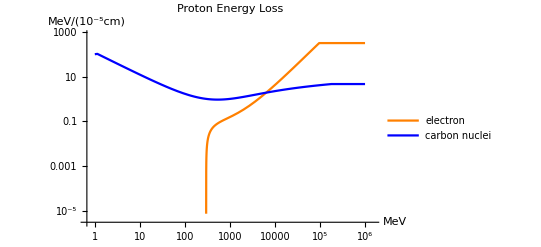

```mathematica
Show[Plotprotonelectron,Plotprotoncarbon,AxesLabel->{"MeV","MeV/(10^-5cm)"},PlotLabel->"Proton Energy Loss"]
```

```mathematica
Convert[(Mega ElectronVolt)^2*1/(200 Mega ElectronVolt*Fermi), (Mega ElectronVolt)/Centimeter]//N
```

(5.×10^10 ElectronVolt Mega)/Centimeter

```mathematica
Plotelectronelectron=LogLogPlot[dedxpauli*5.*^5/.{M->0.511,me->0.511,α->1/137,mπ->0.511,Z->1,n->8},{Eπ,1,10^6},PlotStyle->{Orange,Thick},PlotLegends->{"electron"}];
```

```mathematica
Plotelectroncarbon=LogLogPlot[dEdxcarbonmax*5.*^5/.{n->0.8,me->0.511,M->11180,α->1/137,mπ->0.511,Z->6},{Eπ,1,10^6},PlotStyle->{Blue,Thick},PlotLegends->{"carbon nuclei"}];
```

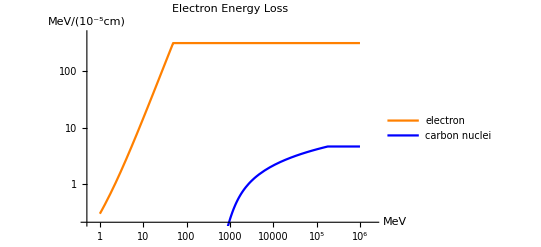

```mathematica
Show[Plotelectronelectron,Plotelectroncarbon,AxesLabel->{"MeV","MeV/(10^-5cm)"},PlotLabel->"Electron Energy Loss"]
```

```mathematica
Plotmuonelectron=LogLogPlot[dedxpauli*5.*^5/.{M->0.511,me->0.511,α->1/137,mπ->100,Z->1,n->8},{Eπ,1,10^6},PlotStyle->{Orange,Thick},PlotLegends->{"electron"}];
```

```mathematica
Plotmuoncarbon=LogLogPlot[dEdxcarbonmax*5.*^5/.{n->0.8,me->0.511,M->11180,α->1/137,mπ->100,Z->6},{Eπ,1,10^6},PlotStyle->{Blue,Thick},PlotLegends->{"carbon nuclei"}];
```

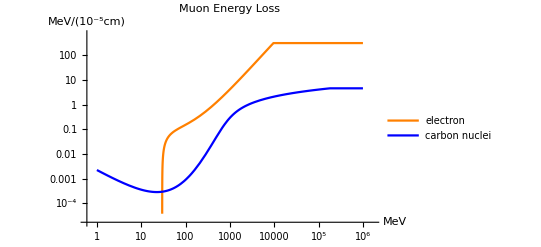

```mathematica
Show[Plotmuonelectron,Plotmuoncarbon,AxesLabel->{"MeV","MeV/(10^-5cm)"},PlotLabel->"Muon Energy Loss"]
```

```mathematica
Convert[(6Pi*6*1/137*n/((3 Pi^2 n)^(1/3)))^(-1/2)/.{n->10^26/Centimeter^3},Fermi]//N
```

41706.5 Fermi

```mathematica
1/(0.511Mega ElectronVolt)*200 Mega ElectronVolt*Fermi
```

391.389 Fermi

```mathematica
Convert[BohrRadius,Fermi]
```

52917.7 Fermi